## KERNEL-DOCS

## Preamble

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<Geometry`
```

## Object Specifications

### POINT

{{{0,{{2,2},{4,4},{0,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

{RGBColor[1, 0, 0],Opacity[1],{PointSize[0.0125],Point[{{2,2},{4,4},{0,4}}]}}

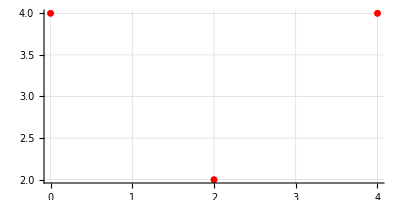

```mathematica
newGeo[{0,{{2,2},{4,4},{0,4}}}]
newGeo[{0,{{2,2},{4,4},{0,4}}}]//toGL
newGeo[{0,{{2,2},{4,4},{0,4}}}]//toGL//gr1
```

### POLYGON

{{{1,{{2,2},{4,4},{0,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}],Polygon[…]}}

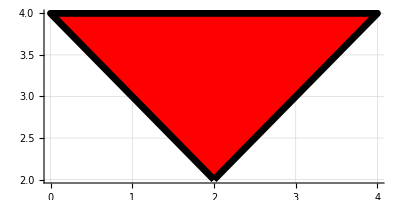

```mathematica
newGeo[{1,{{2,2},{4,4},{0,4}}}]
newGeo[{1,{{2,2},{4,4},{0,4}}}]//toGL
newGeo[{1,{{2,2},{4,4},{0,4}}}]//toGL//gr1
```

### CIRCLE

{{{2,{{2,2},{4,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

{RGBColor[1, 0, 0],Opacity[1],{Thickness[0.0125],Dashing[{2 π,2 π}],Circle[{2,2},2 √2]}}

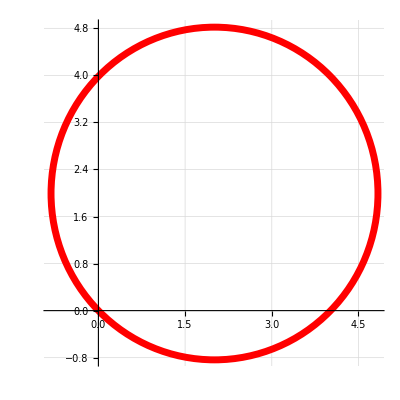

```mathematica
newGeo[{2,{{2,2},{4,4}}}]
newGeo[{2,{{2,2},{4,4}}}]//toGL
newGeo[{2,{{2,2},{4,4}}}]//toGL//gr1
```

### LINE

{{{3,{{2,2},{4,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

{RGBColor[1, 0, 0],Opacity[1],{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}],Line[{{2,2},{4,4}}]}}

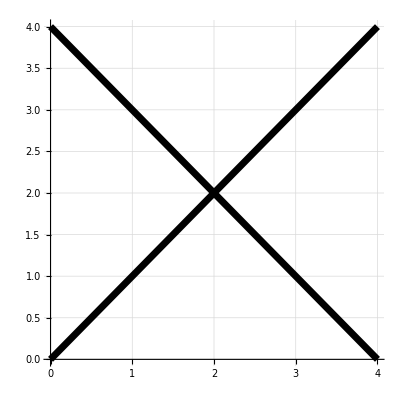

```mathematica
newGeo[{3,{{2,2},{4,4}}}]
newGeo[{3,{{2,2},{4,4}}}]//toGL
newGeo[{3,{{2,2},{4,4}}}]//toGL//gr;
fig1=newGeo[{3,{{2,2},{4,4}}}];
fig2={fig1,rot3[fig1,{3/2 Pi,{2,2}}]};
{fig2,rot3[fig2,{2/2 Pi,{2,2}}]}//toGL//gr1
```

### DISK

{{{4,{{2,2},{4,4}}},{RGBColor[1, 0, 0],1}},{GrayLevel[0],1,0.0125,2 π,2 π}}

{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}],Disk[{2,2},2 √2]}}

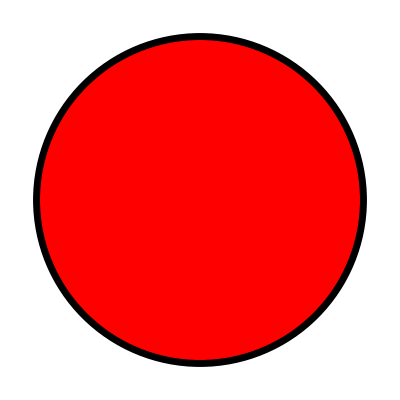

```mathematica
newGeo[{4,{{2,2},{4,4}}}]
newGeo[{4,{{2,2},{4,4}}}]//toGL
newGeo[{4,{{2,2},{4,4}}}]//toGL//gr
```

### FILLEDCURVE

```mathematica
newGeo[{5,{{2,2},{4,4}}}];
newGeo[{5,{{2,2},{4,4}}}]//toGL
newGeo[{5,{{2,2},{3,3},{3,5},{4,4}}}]//toGL//gr
```

{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[Directive[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}]],FilledCurve[BezierCurve[{{2,2},{4,4}}]]}}

-Graphics-

## Object Transformations

### TRANSLATION

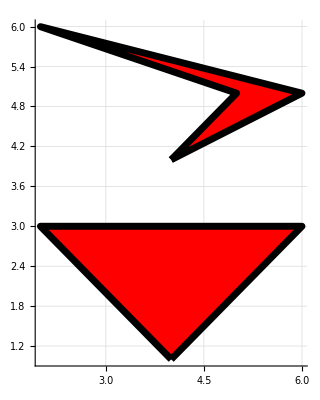

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
tra3[fig12,{2,-1}]//toGL//gr1
```

### ROTATION

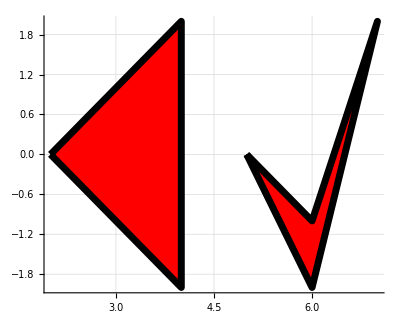

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
rot3[fig12,{3/2 Pi,{1,1}}]//toGL//gr1
```

### REFLECTION

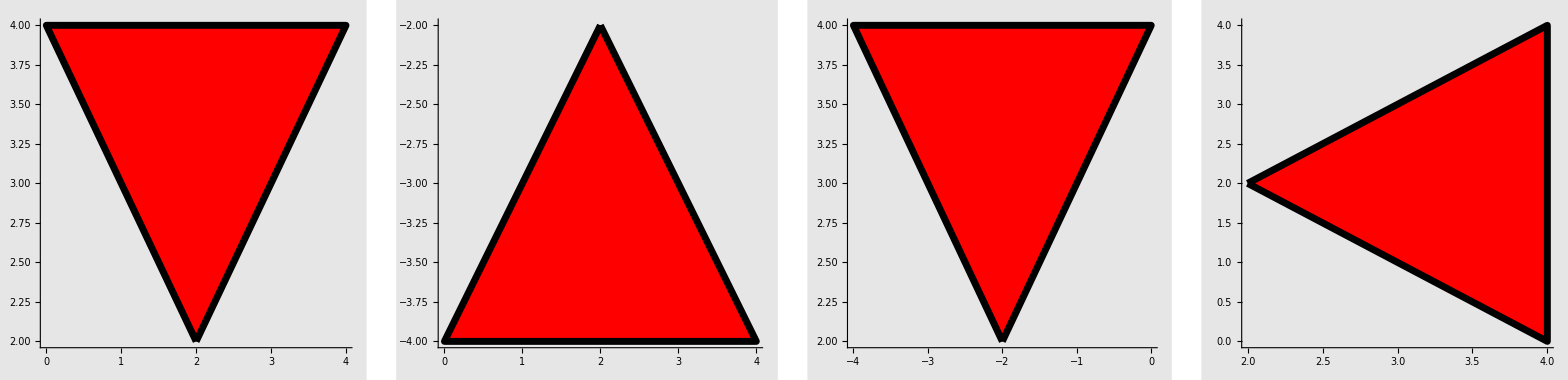

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
GraphicsRow[
{fig1//toGL//gr2,
ref3[fig1,{{0,1},{0,0}}]//toGL//gr2 (* Reflection in X-axis *),
ref3[fig1,{{1,0},{0,0}}]//toGL//gr2 (* Reflection in Y-axis *),
ref3[fig1,{{-1,1},{0,0}}]//toGL//gr2 (* Reflection in line Y=X *)}
]
```

### CONJUGATION

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
cnj3[cnj3[fig1]]//toGL//gr1
```

-Graphics-

### SCALING

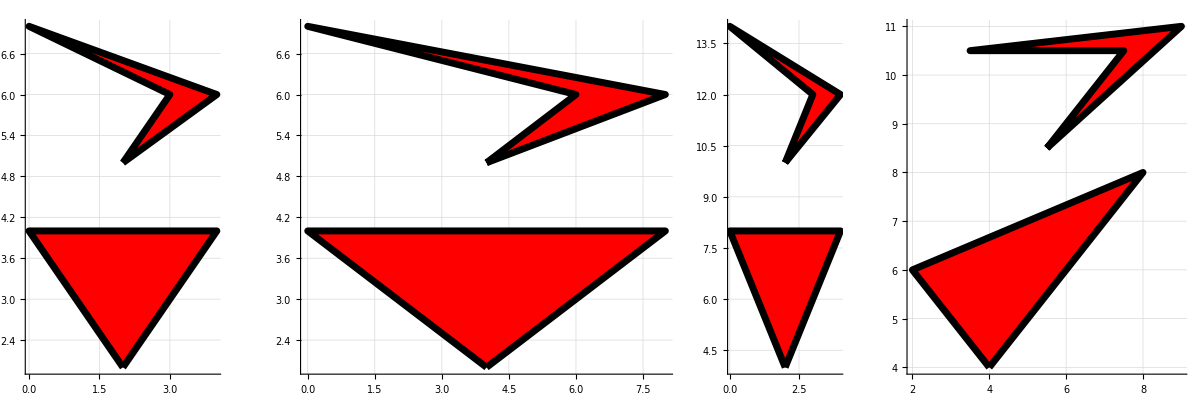

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
fig2=newGeo[{1,{{2,5},{4,6},{0,7},{3,6}}}];
fig12={fig1,fig2};
GraphicsRow[
{fig12//toGL//gr1,
sca3[fig12,{2,{1,0}}]//toGL//gr1,
sca3[fig12,{2,{0,1}}]//toGL//gr1,
sca3[fig12,{2,{1,1}}]//toGL//gr1}
]
```

## Property Updates

### FACE COLOR

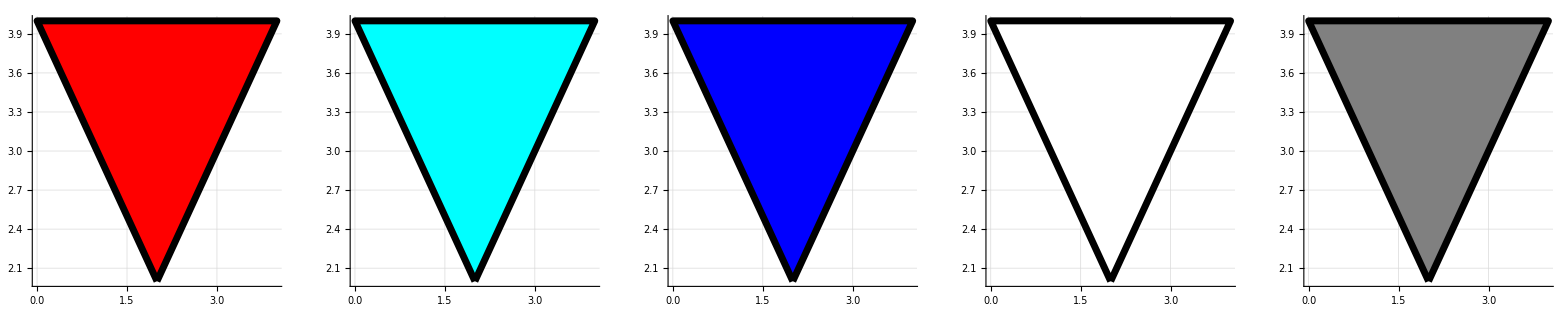

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
GraphicsRow[
{fig1//toGL//gr1,
repCol[fig1,{Cyan}]//toGL//gr1,
repCol[fig1,{Blue}]//toGL//gr1,
repCol[fig1,{White}]//toGL//gr1,
repCol[fig1,{Gray}]//toGL//gr1
}
]
```

### LINE COLOR

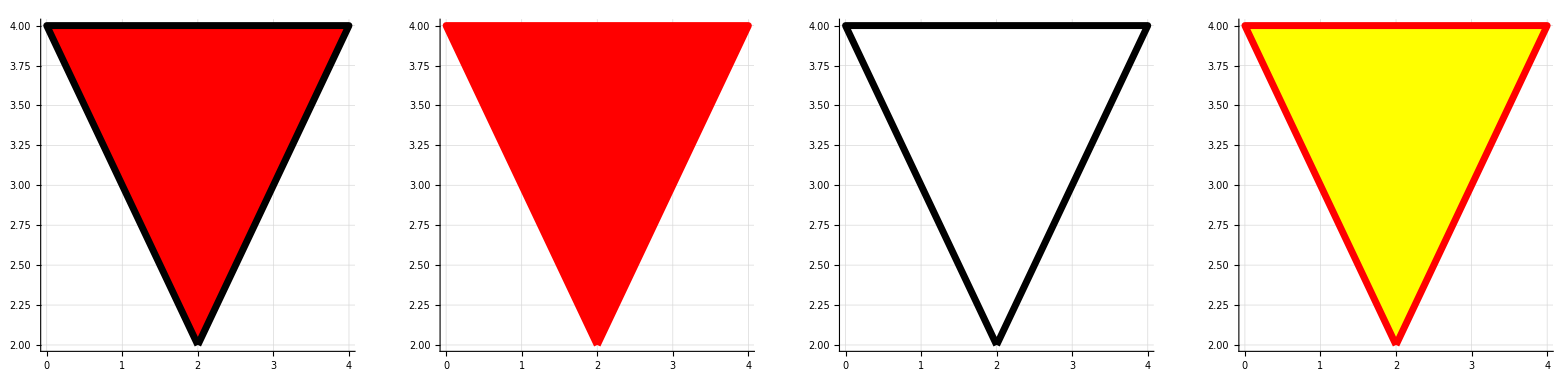

```mathematica
fig1=newGeo[{1,{{2,2},{4,4},{0,4}}}];
GraphicsRow[
{fig1//toGL//gr1,
repLineCol[fig1,{Red}]//toGL//gr1,
repCol[fig1,{White}]//toGL//gr1,
repLineCol[repCol[fig1,{Yellow}],{Red}]//toGL//gr1
}
]
```

## OTHER STUFF

## Apps

### Case 1

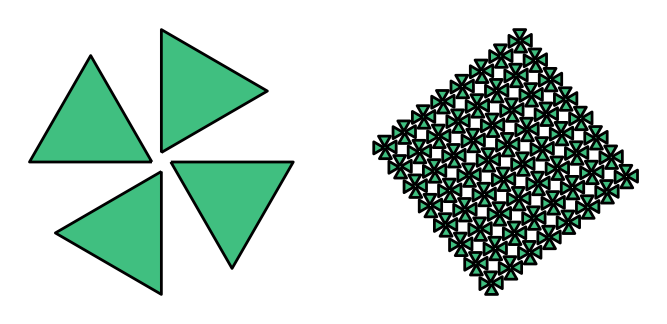

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}]}]

dpoly:=tra3[newGeo[6],{2,1}]
dpoly:={{{1,{{0,0},{1,0},{1,1},{.5,4.0},{0,1}}},{White,1}},{Black,1,.005,2 π,2 π}}

dpoly:={tra3[newGeo[3,RGBColor[.25,.75,.5,.5]][[1]],{1,1}],{Black,1,.005,2 π,2 π}}
GraphicsRow[{Graphics[Nest[teil,dpoly,1]//toGL],
Graphics[rot3[Nest[teil,dpoly,4],{30 Degree,{0,0}}]//toGL]}]
```

```mathematica
nGonAtEdge3[fig_,{m_,n_}]:=trf3[
trf3[
newGeo[n],
toUnit[toEdges[newGeo[n]][[1,1,1,2]]]//N
],
toVector[toEdges[fig][[m,1,1,2]]]
]
```

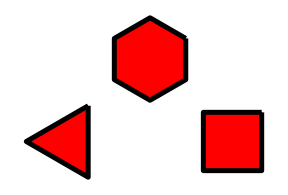

```mathematica
dpoly1:=tra3[newGeo[3],{0,0}]
dpoly2:=tra3[newGeo[4],{4,0}]
dpoly3:=tra3[newGeo[6],{2,2}]
Graphics[{dpoly1,dpoly2,dpoly3}]//toGL
```

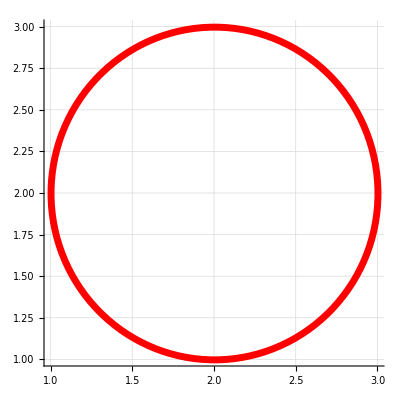

```mathematica
cCircle[{2,2},1]//toGL//gr1
```

### Case 2

```mathematica
cCircle[{5,5},1.5]//toGL
```

{RGBColor[0, 1, 1],Opacity[1],{Thickness[0.0025],Dashing[{2 π,2 π}],Circle[{5,5},1.5]}}

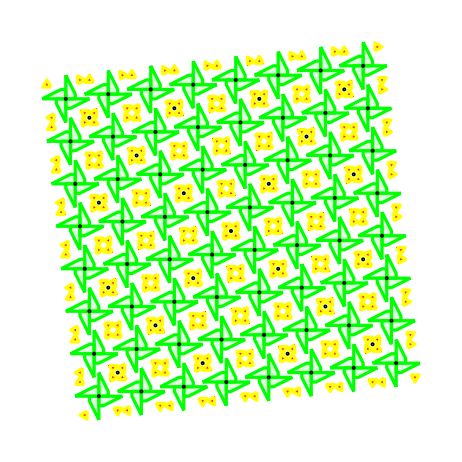

```mathematica
teil[figke_]:= Module[{rotp},
rotp=2mid[figke];
{figke,rot3[figke,{π/2,rotp}],rot3[figke,{π,rotp}],rot3[figke,{3 π /2,rotp}],
repCol[cCircle[rotp,.25],{Black}]
}]

dpolyA:={tra3[newGeo[3,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
dpolyB:={{{1,{{4,0},{4,5},{2,5},{2,4}}},{LightGreen,1}},{Green,1,.005,2 π,2 π}}
Nest[teil,{dpolyB,dpolyA},4]//toGL//gr
```

### Case 3

```mathematica
ind:=Tuples[Composition@@{sym4ref,sym4rot},3]
```

```mathematica
dpoly:={{{1,{{0,0},{0.5,0.2},{1,1},{0.2,0.9}}},{RGBColor[1, 0.9500000000000001, 0],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{1,0},{0.7,1},{0.3,1}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={{{1,{{0,0},{0.25,0},{0.5,0.25},{0.5,.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
sym4rot[sym4ref[dpoly]]//toGL//gr1
```

-Graphics-

```mathematica
Table[ind[[k]][dpoly]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Case 4 ( IN-DEVELOPMENT )

```mathematica
dpoly0:={{{1,{{0.25,0.0},{0.5,0.0},{0.5,0.75},{0.75,0.75},{0.75,1.0},{0.0,1.0},{0.0,0.75},{0.25,0.75}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyA:={{{1,{{0.5,0},{1,0.5},{1,1},{0.5,0.5},{0,1},{0,.5}}},{RGBColor[0.87, 0.87, 0.87, 0.9],1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyB:={{{1,{{0,0},{0.5,0},{0,0.5}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpolyC:={{{1,{{0.5,0},{1,0},{1,0.5}}},{Cyan,1}},{RGBColor[0.06, 0.06, 0.06],1,0.005,2 π,2 π}}
dpoly:={dpolyA,dpolyB,dpolyC}
dpoly//toGL//gr1;
sym4ovr1[dpoly]//toGL//gr1
```

-Graphics-

```mathematica
sym4ovr1[figke_]:=Module[{rotp},
rotp={1,1};
tra3[Scale[
{
figke,
rot3[ref3[figke,{{1,0},rotp}],{π,{1.5,0.5}}],
tra3[figke,{1,1}],
tra3[rot3[ref3[figke,{{1,0},rotp}],{π,{1.5,0.5}}],{-1,1}]
},
.5],{-.5,-.5}]]
```

```mathematica
ind:=Tuples[Composition@@{sym4rot,sym4ref,sym4ovr1},3]
Table[ind[[k]][dpoly]//toGL//gr,{k,1,Length[ind]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ind//TableForm
```

sym4rot@*sym4rot@*sym4rot
sym4rot@*sym4rot@*sym4ref
sym4rot@*sym4rot@*sym4ovr1
sym4rot@*sym4ref@*sym4rot
sym4rot@*sym4ref@*sym4ref
sym4rot@*sym4ref@*sym4ovr1
sym4rot@*sym4ovr1@*sym4rot
sym4rot@*sym4ovr1@*sym4ref
sym4rot@*sym4ovr1@*sym4ovr1
sym4ref@*sym4rot@*sym4rot
sym4ref@*sym4rot@*sym4ref
sym4ref@*sym4rot@*sym4ovr1
sym4ref@*sym4ref@*sym4rot
sym4ref@*sym4ref@*sym4ref
sym4ref@*sym4ref@*sym4ovr1
sym4ref@*sym4ovr1@*sym4rot
sym4ref@*sym4ovr1@*sym4ref
sym4ref@*sym4ovr1@*sym4ovr1
sym4ovr1@*sym4rot@*sym4rot
sym4ovr1@*sym4rot@*sym4ref
sym4ovr1@*sym4rot@*sym4ovr1
sym4ovr1@*sym4ref@*sym4rot
sym4ovr1@*sym4ref@*sym4ref
sym4ovr1@*sym4ref@*sym4ovr1
sym4ovr1@*sym4ovr1@*sym4rot
sym4ovr1@*sym4ovr1@*sym4ref
sym4ovr1@*sym4ovr1@*sym4ovr1

## Test Möbius Transformations

```mathematica
FileNameJoin[{$InstallationDirectory,"SystemFiles","Components","AutoCompletionData","Main","OptionValues"}]
```

C:\Program Files\Wolfram Research\Mathematica\12.3.1\SystemFiles\Components\AutoCompletionData\Main\OptionValues

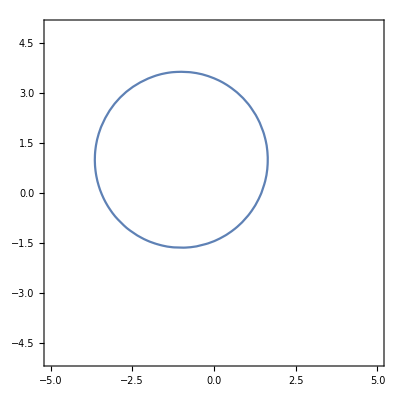

```mathematica
ClearAll[x,y]
ContourPlot[x^2+y^2+2x-2y-5==0,{x,-5,5},{y,-5,5},Axes->True]
```

```mathematica
(3z Conjugate[z]//ComplexExpand)/.z:>x+I y//Expand
```

```mathematica
z Conjugate[z]/. z-> x+I y
```

(x+ⅈ y) (Conjugate[x]-ⅈ Conjugate[y])

```mathematica
3(x+I y)(x-I y)//Expand
```

3 x^2+3 y^2

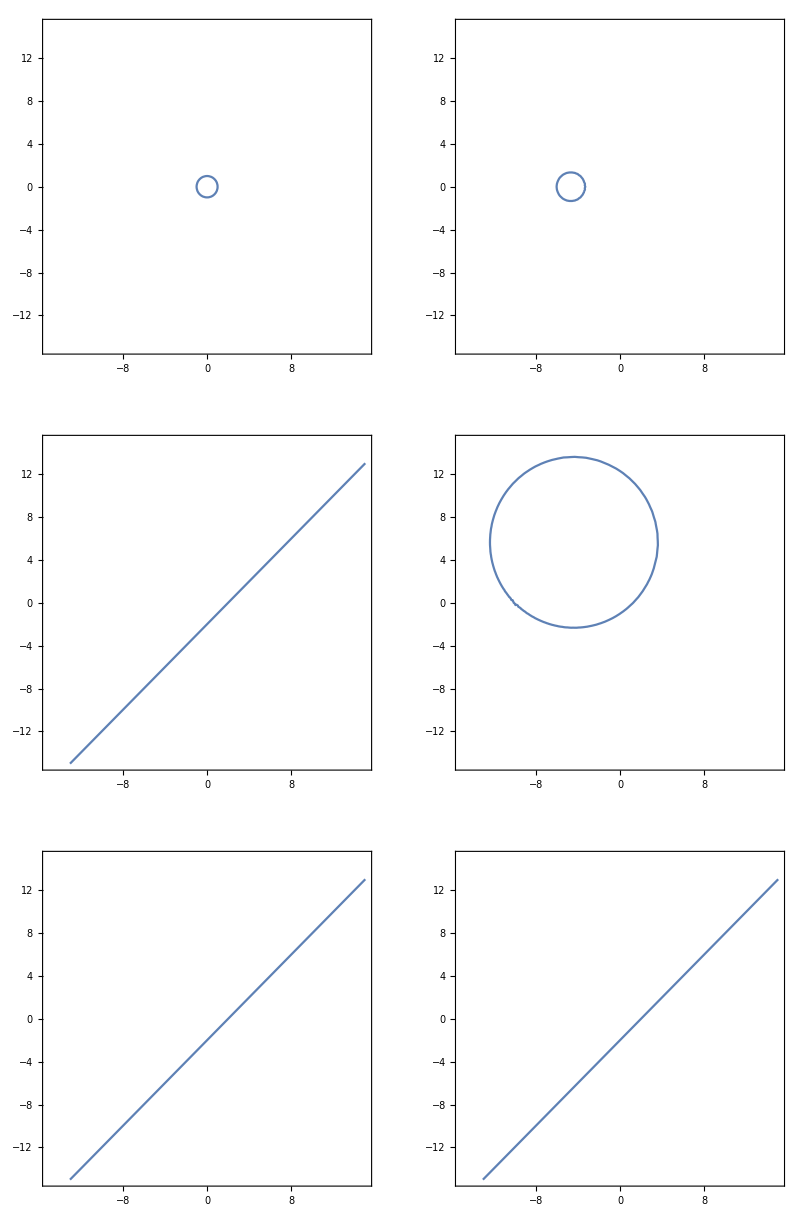

```mathematica
eqn1=ComplexExpand[z Conjugate[z]-1/.z->(1z+0)/(0z+1),z]/.{Re[z]->x,Im[z]->y};
eqn2=ComplexExpand[z Conjugate[z]-1/.z->(0.5z+1)/(1z+4),z]/.{Re[z]->x,Im[z]->y}//FullSimplify;
eqn3=ComplexExpand[Im[z]-Re[z]+2/.z->(1z+0)/(0z+1),z]/.{Re[z]->x,Im[z]->y};
eqn4=ComplexExpand[Im[z]-Re[z]+2/.z->(z+1)/(.1z+1),z]/.{Re[z]->x,Im[z]->y};
eqn5=ComplexExpand[Im[z]-Re[z]+2/.z->(z+0)/(0z+1),z]/.{Re[z]->x,Im[z]->y};
eqn6=ComplexExpand[Im[z]-Re[z]+2/.z->(z+2)/(.1z+1)/.z->(1z-2)/(-.1z+1),z]/.{Re[z]->x,Im[z]->y};

a=15;
GraphicsGrid[{
{
ContourPlot[eqn1==0,{x,-a,a},{y,-a,a},Axes->True],
ContourPlot[eqn2==0,{x,-a,a},{y,-a,a},Axes->True]},
{ContourPlot[eqn3==0,{x,-a,a},{y,-a,a},Axes->True],
ContourPlot[eqn4==0,{x,-a,a},{y,-a,a},Axes->True]},
{ContourPlot[eqn5==0,{x,-a,a},{y,-a,a},Axes->True],
ContourPlot[eqn6==0,{x,-a,a},{y,-a,a},Axes->True]
}
}]
```

```mathematica
z Conjugate[z]-1/.z->(1z-5)/(0z+5)//Expand
```

-z/5-Conjugate[z]/5+1/25 z Conjugate[z]

```mathematica
m:={{4,9},{11,25}};
t:={{1,1},{0,1}};
```

```mathematica
m//mf
m.Inverse[t]//mf
m.Inverse[t].Inverse[t]//mf
m.MatrixPower[Inverse[t],5]//mf
```

(4 | 9
11 | 25)

(4 | 5
11 | 14)

(4 | 1
11 | 3)

(4 | -11
11 | -30)

```mathematica
Clear[a,b,c,d]
ma={{a,b},{c,d}};
mt={{1,1},{0,1}};
ms={{0,-1},{1,0}};
mst={{0,-1},{1,1}};
```

```mathematica
mst.ma.Inverse[mst]//mf
```

(-c+d | -c
a-b+c-d | a+c)

```mathematica
mt.{1,0}.Inverse[mt]
```

{1,-1}

```mathematica
maa={{5,2},{-2,3}};
maa={{b+d,b},{-b,d}};
maa1={{a,-c},{c,a+c}};
{mst.maa,maa.mst}
{mst.maa1,maa1.mst}
```

{{{b,-d},{d,b+d}},{{b,-d},{d,b+d}}}

{{{-c,-a-c},{a+c,a}},{{-c,-a-c},{a+c,a}}}

```mathematica
mm={{1,0,1,-1},{0,1,1,0},{1,-1,0,-1},{1,0,1,-1}};
```

```mathematica
MatrixRank[mm]
NullSpace[mm]
RowReduce[mm]
```

2

{{1,0,0,1},{-1,-1,1,0}}

{{1,0,1,-1},{0,1,1,0},{0,0,0,0},{0,0,0,0}}

```mathematica
mm.{-1,-1,1,0}
```

{0,0,0,0}

```mathematica
maa2=a mst+b IdentityMatrix[2];
maa2=a IdentityMatrix[2] + b mst+c Inverse[mst]
mst.maa2//mf
maa2.mst//mf
```

{{a+c,-b+c},{b-c,a+b}}

(-b+c | -a-b
a+b | a+c)

(-b+c | -a-b
a+b | a+c)

```mathematica
mst//mf
Inverse[mst]//mf
```

(0 | -1
1 | 1)

(1 | 1
-1 | 0)

```mathematica
Graphics3D[{Opacity[0.6],Octahedron[],Circumsphere[Octahedron[]]}]
```

-Graphics3D-

## Lines-UZT-1

```mathematica
p1:={0,0};
p2:={3,1};
p3:={1,3};
p4:={4,3};
p5:={-2,3};
Graphics[{
Arrow[{p1,p5}],
Line[{p1,p2}],
HalfLine[{p1,p4}],
Dashed,InfiniteLine[{p1,p3}]
},
AxesOrigin->{0,0},Axes->True,AxesLabel->{"X","Y"},
PlotRange->{{-5,5},{-5,5}}]
```

-Graphics-

```mathematica
tra3cp[figs_,t_]:={figs,figs/.f:pnt:>TranslationTransform[t][f]}
```

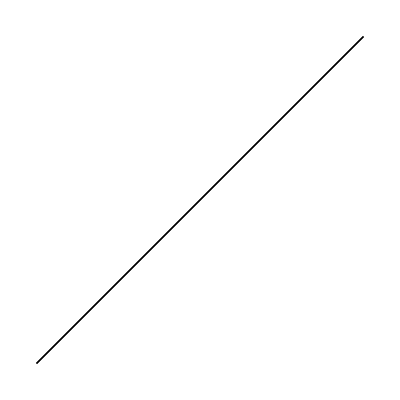

```mathematica
tra3cp[{Line[{{0,0},{1,1}}]},{0,0}]//toGL//Graphics
```

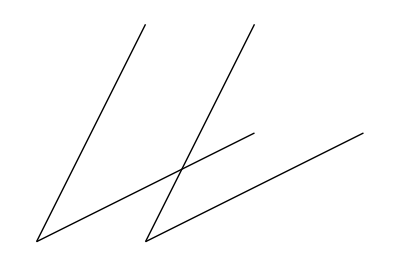

```mathematica
tra3cp[{Line[{{0,0},{4,2}}],Line[{{0,0},{2,4}}]},{-2,0}]//toGL//Graphics
```

```mathematica
trans[figke_]:= Module[{},
{
figke,
tra3cp[figke,{1,0}]
}
]
line:={Line[{{0,0},{4,2}}]}
```

```mathematica
Fold[tra3cp,line,Table[{1,1},{k,1}]]//tf
```

Line[{{0,0},{4,2}}]
Line[{{1,1},{5,3}}]

```mathematica
Fold[tra3cp,line,Table[{k,k},{k,2}]]//tf
```

Line[{{0,0},{4,2}}] | Line[{{1,1},{5,3}}]
Line[{{2,2},{6,4}}] | Line[{{3,3},{7,5}}]

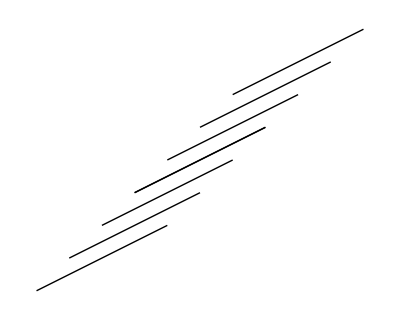

```mathematica
Fold[tra3cp,line,Table[{k,k},{k,3}]]//toGL//Graphics
```

## Lines-UZT-2

```mathematica
Table[ReIm[ⅇ^((k 2 Pi I)/4)],{k,0,3}]//tf
Table[ReIm[ⅇ^((k 2 Pi I)/8)],{k,0,7}]//tf
```

1 | 0
0 | 1
-1 | 0
0 | -1

1 | 0
1/(√2) | 1/(√2)
0 | 1
-1/(√2) | 1/(√2)
-1 | 0
-1/(√2) | -1/(√2)
0 | -1
1/(√2) | -1/(√2)

```mathematica
lines[n_]:=Map[Line[{{0,0},#}]&,Table[ReIm[ⅇ^((k 2 Pi I)/n)],{k,0,n-1}]]
{{{1,{{0,0},#}},{White,1}},{Black,1,.005,2 π,2 π}};
lines[n_]:=Map[{{{1,{{0,0},#}},{Red,1}},{Blue,1,.005,2 π,2 π}}&,Table[ReIm[ⅇ^((k 2 Pi I)/n)],{k,0,n-1}]]
```

```mathematica
GraphicsRow[{
lines[18]//toGL//Graphics
}]
```

-Graphics-

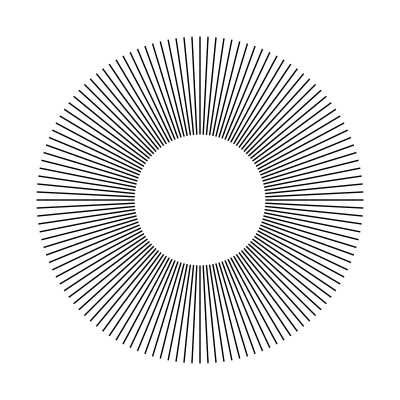

```mathematica
lines2[n_]:=Map[Line[{0.4#[[2]],#[[2]]}]&,Table[{(k+1)/n ReIm[ⅇ^((k 2 Pi I)/n)],ReIm[ⅇ^((k 2 Pi I)/n)]},{k,0,n-1}]]
lines2[128]//toGL//Graphics
```

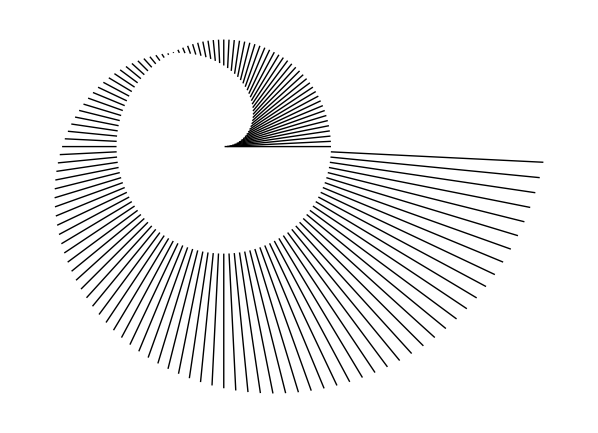

```mathematica
lines3[n_]:=Map[Line[{#[[1]],#[[2]]}]&,Table[{((3k+1)/n)ReIm[ⅇ^((k 2 Pi I)/n)],ReIm[ⅇ^((k 2 Pi I)/n)]},{k,0,n-1}]]
lines3[128]//toGL//Graphics
```

```mathematica
Integrate[Sin[x] x^2,{x,a,b}]
```

(-2+a^2) Cos[a]-(-2+b^2) Cos[b]-2 a Sin[a]+2 b Sin[b]

## Lines-UZT-3-Definition-for-KickOff

### Scaled

```mathematica
Graphics[{Disk[Scaled[{.25,.25}],1]},Frame->True,PlotRange->{{0,10},{0,10}}]
```

-Graphics-

```mathematica
Graphics[Disk[Scaled[{.50,.50}],10],PlotRange->{{-100,100},{-100,100}},Frame->True,AxesOrigin->{0,0},Axes->True]
```

-Graphics-

### Offset

## OLD-Preamble

```mathematica
(* AppendTo[$Path,"C:\\Users\\Nilo\\__DATA\\Mega\\DATA\\eclipse-workspace\\Geometry"];
<<Geometry` *)
```

```mathematica
AppendTo[$Path,"C:\\Users\\deroo\\__DATA\\MEGA\\DATA\\git\\MFDSNT\\Mathematica Notebooks"];
<<BKPNumberTheory`
<<TestAlgebra` 
<<Geometry`
```

Get::noopen: Cannot open TestAlgebra`.

$Failed

Get::noopen: Cannot open Geometry`.

$Failed

```mathematica
nCollatz[16]
```

{16,8,4,2,1}

## tmp-1

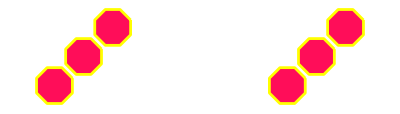

```mathematica
dpolyA:={tra3[newGeo[8,RGBColor[1,.05,.35,.1]][[1]],{1,1}],{Yellow,1,.005,2 π,2 π}}
dpolyA;
dpolyA//toGL;
{dpolyA,tra3[dpolyA,{2,2}]}//toGL ;
{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]}//toGL;
{{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]},tra3[{dpolyA,tra3[dpolyA,{1.5,1.5}],tra3[dpolyA,{3.0,3.0}]},{12,0}]}//toGL//gr
```

```mathematica
newGeo[1,Red,{{4,4}}]//toGL
```

newGeo[1,RGBColor[1, 0, 0],{{4,4}}]

```mathematica
{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.05],Dashing[{2 π,2 π}]}],Polygon[…]}}//gr
```

-Graphics-

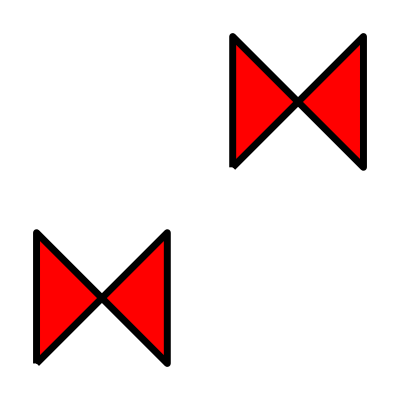

```mathematica
{newGeo[{1,{{0,0},{4,4},{4,0},{0,4}}}],tra3[newGeo[{1,{{0,0},{4,4},{4,0},{0,4}}}],{6,6}]}//toGL//gr
```

```mathematica
CoordinateTransformData[]//tf;
CoordinateChartData[]//tf
```

Bipolar
a | Euclidean | 2
BipolarCylindrical
a | Euclidean | 3
Bispherical
a | Euclidean | 3
Cartesian | Euclidean | 1
Cartesian | Euclidean | 2
Cartesian | Euclidean | 3
Cartesian | Euclidean | 4
Cartesian | Euclidean | 5
Cartesian | Euclidean | 6
Cartesian | Euclidean | 7
Cartesian | Euclidean | 8
Cartesian | Euclidean | 9
Cartesian | Euclidean | 10
CircularParabolic | Euclidean | 3
Confocal | 
α | β | Euclidean | 2
Confocal |  | 
α | β | γ | Euclidean | 3
Confocal |  |  | 
α_1 | α_2 | α_3 | α_4 | Euclidean | 4
Confocal |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | Euclidean | 5
Confocal |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | Euclidean | 6
Confocal |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | Euclidean | 7
Confocal |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | Euclidean | 8
Confocal |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | Euclidean | 9
Confocal |  |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | α_10 | Euclidean | 10
Confocal |  |  |  |  |  |  |  |  |  | 
α_1 | α_2 | α_3 | α_4 | α_5 | α_6 | α_7 | α_8 | α_9 | α_10 | α_11 | Euclidean | 11
ConfocalParaboloidal | 
α | β | Euclidean | 3
Conical | 
b | c | Euclidean | 3
Cylindrical | Euclidean | 3
Elliptic
a | Euclidean | 2
EllipticCylindrical
a | Euclidean | 3
Polar | Euclidean | 2
Hyperspherical | Euclidean | 3
Hyperspherical | Euclidean | 4
Hyperspherical | Euclidean | 5
Hyperspherical | Euclidean | 6
Hyperspherical | Euclidean | 7
Hyperspherical | Euclidean | 8
Hyperspherical | Euclidean | 9
Hyperspherical | Euclidean | 10
Hyperspherical | Euclidean | 11
OblateSpheroidal
a | Euclidean | 3
ParabolicCylindrical | Euclidean | 3
PlanarParabolic | Euclidean | 2
ProlateSpheroidal
a | Euclidean | 3
Spherical | Euclidean | 3
Toroidal
a | Euclidean | 3
Standard | Sphere
R | 1
Standard | Sphere
R | 2
Standard | Sphere
R | 3
Standard | Sphere
R | 4
Standard | Sphere
R | 5
Standard | Sphere
R | 6
Standard | Sphere
R | 7
Standard | Sphere
R | 8
Standard | Sphere
R | 9
Standard | Sphere
R | 10
Stereographic | Sphere
R | 1
Stereographic | Sphere
R | 2
Stereographic | Sphere
R | 3
Stereographic | Sphere
R | 4
Stereographic | Sphere
R | 5
Stereographic | Sphere
R | 6
Stereographic | Sphere
R | 7
Stereographic | Sphere
R | 8
Stereographic | Sphere
R | 9
Stereographic | Sphere
R | 10

```mathematica
CoordinateTransform[{"Cartesian"->"Polar",2},{1,-1}]
CoordinateTransform[{"Polar"->"Cartesian",2},{√2,-π/4}]
```

{√2,-π/4}

{1,-1}

```mathematica
FromPolarCoordinates[ToPolarCoordinates[{1/(√2),1/(√2)}]]
FromSphericalCoordinates[ToSphericalCoordinates[{{x,y,z},{1,0,0}}]]
```

{1/(√2),1/(√2)}

{{x,y,z},{1,0,0}}

```mathematica
CoordinateTransform[{"Cartesian"->"Polar",2},{1/√2,-1/√2}]
```

{1,-π/4}

```mathematica
1/((1/√2)+I(1/√2))
```

(1-ⅈ)/(√2)

```mathematica
FromPolarCoordinates[{R,θ}]
ToPolarCoordinates[FromPolarCoordinates[{R,θ}]]
ToPolarCoordinates[FromPolarCoordinates[{R,θ}]]//FullSimplify
```

{R Cos[θ],R Sin[θ]}

{√(R^2 Cos[θ]^2+R^2 Sin[θ]^2),ArcTan[R Cos[θ],R Sin[θ]]}

{√(R^2),ArcTan[R Cos[θ],R Sin[θ]]}

```mathematica
D[Exp[x],x]==Exp[x]
```

True

```mathematica
168-(18+17+15+13+12+15+14)-4
```

60

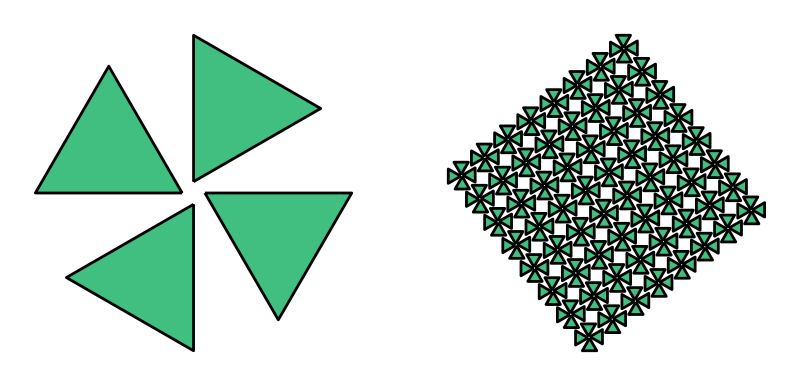

```mathematica
dpoly:={tra3[newGeo[3,RGBColor[.25,.75,.5,.5]][[1]],{1,1}],{Black,1,.005,2 π,2 π}}
GraphicsRow[{Graphics[Nest[teil,dpoly,1]//toGL],
Graphics[rot3[Nest[teil,dpoly,4],{30 Degree,{0,0}}]//toGL]}]
```

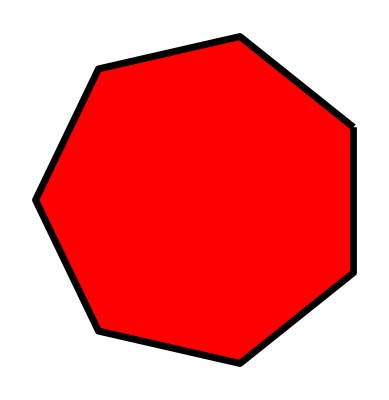

```mathematica
newGeo[7]//toGL//gr
```

```mathematica
nGonAtEdge3[fig_,{m_,n_}]:=trf3[
trf3[
newGeo[n],
toUnit[toEdges[newGeo[n]][[1,1,1,2]]]//N
],
toVector[toEdges[fig][[m,1,1,2]]]
]
```

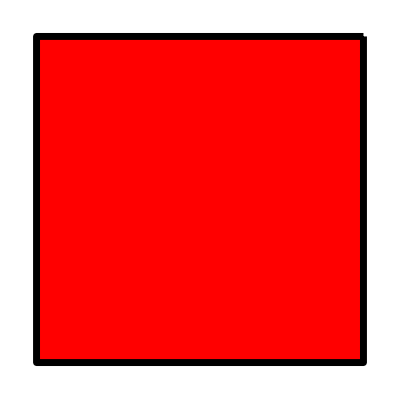

```mathematica
nGonAtEdge3[newGeo[4],{3,4}]//toGL//gr
```

## notes

## tmp-1

```mathematica
newGeo[{1,{{2,2},{4,4},{0,4}}}]//toGL
```

{RGBColor[1, 0, 0],Opacity[1],{EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}],Polygon[…]}}

```mathematica
EdgeForm[{GrayLevel[0],Opacity[1],Thickness[0.0125],Dashing[{2 π,2 π}]}]
```

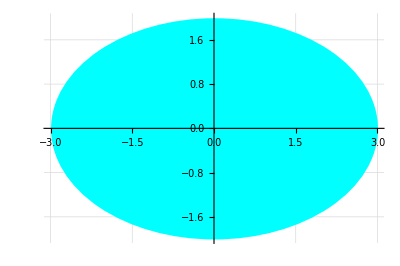

```mathematica
{Cyan,Ellipsoid[{0,0},{3,2}]}//gr1
```

```mathematica
EntityValue[
Entity["Country","Netherlands"],
EntityProperty["Country","Population"]
]
```

17591475 people

```mathematica
EntityValue[
Entity["Country","Russia"],
EntityProperty["Country","Population"]
]
```

144400000 people

```mathematica
18+17+15+13+12+15+14
14+12+12+6+5+7+8
```

104

64

```mathematica
6+5+3+1+3+2
```

20

```mathematica
2+0+0-6-7-5 -4
```

-20

```mathematica
EntityProperties["Country"]//tf
```

active home listings
adjusted net national income
seasonal bank borrowings from Fed, plus adjustments
regions
adult population
obese adults
number of aggravated assaults
rate of aggravated assault
aggregate home value
aggregate home value, householder 15 to 24 years
aggregate home value, householder 25 to 34 years
aggregate home value, householder 35 to 64 years
aggregate home value, householder 65 years and over
aggregate household income
aggregate weekly hours index
agricultural irrigated land fraction
agricultural land fraction
agricultural production index
agricultural production per capita index
agricultural products
consumption
consumption per capita
harvest area
harvest area per capita
production
production per capita
average yield
yield per capita
arrivals by air
aircraft carriers
air force
airports
air transport
alcohol fuel
total primary energy
alternate names
AM radio stations
annual annulments
annual births
annual deaths
annual divorces
annual HIV/AIDS deaths
annual marriages
antenatal care coverage
annual-crop land area
annual-crop land fraction
total area
armored infantry fighting vehicles
armored personnel carriers
army
artillery
attack helicopters
automobile production
average home listing price
average hourly earnings
average length of stay
average number of meetings with tax officials
average time to clear exports through customs
average weekly hours
average weekly overtime hours
aviation gasoline
bankers acceptance rate
bank prime loan rate
bank prime loan rate changes
benefits cost index
birth rate fraction
births attended by skilled health personnel
births by caesarean section
book titles published
bordering countries/regions
shared border lengths
full boundary length
burden of customs procedure
number of burglaries
rate of burglary
business activity index
professional arrivals
business entry rate
business extent of disclosure
calling code
capacity utilization rate
capital city
capital location
S&P/Case-Shiller home price index
central bank intervention
certificate of deposit
changes in inventories
checkable deposits
chemicals fraction of manufacturing value added
child employment
child population
vitamin A supplementation
children not enrolled in schools
overweight children
antimalarial treatment for fever
stunted children
underweight children
children with ARI symptoms taken to facility
diarrheal treatment with ORT
children sleeping under insecticide-treated nets
cinema attendance
number of cinemas
cinema seats
civilian employment population ratio
civilian labor force
civilian participation rate
civilian unemployment rate
classes
climate types
lignite brown coal
coal
coal
coast guard
coastline length
commercial banks assets
commercial banks credit
commercial paper
commercial paper of nonfinancial companies
community and traditional health workers
community and traditional health workers per capita
compensation per hour index
school completion rate
prevalence of condom use by young people
construction value added
consumer credit
consumer price index
consumer sentiment
container port traffic
continent
contraceptive prevalence
contributing family workers
contributing family workers fraction
conventional mortgage rate
corporate bond yield
corporate capital consumption adjustment
corporate cash flow
corporate dividends
corporate inventory valuation adjustment
corporate profits
corporate proprietors income
typical cost of business start up procedures
typical cost to export one container
typical cost to import one container
country code
consumer price index
CPIA rating
credit depth of information
total rate of crime
total number of crimes
perennial-crop land area
perennial-crop land fraction
currency code
currency in circulation
currency name
currency short name
currency unit
current account
current account balance
current expenditure on health
average daily hotel stays
daily newspaper circulation
death rate fraction
debt measure
DEC alternative conversion factor
demand deposits
dentistry personnel
dentistry personnel per capita
dependencies
dependency parent
deposit interest rate
deposits with Federal Reserve banks
destroyers
discount rate changes
discount window borrowing
discrepancy in expenditure estimate of GDP
disposable personal income
typical documents required per export shipment
typical documents required per import shipment
improved drinking water sources
natural gas
natural gas
ease of doing business
economic aid
economically active children
total school duration
effective federal funds rate
elderly population
electrical grid frequency
electrical grid plug images
electrical grid plug codes
electrical grid socket images
electrical grid socket codes
electrical grid voltages
electricity from biomass
electricity from fossil fuels
geothermal electricity
hydroelectric electricity
pumped-storage hydroelectricity
nuclear electricity
electricity from solar, tide, or waves
total electricity
electricity from renewables
electricity from wind
falling water resources for electric power
emigration rate of tertiary educated
employees compensation
self-employed with employees
employers fraction
employment
employment cost index
employment fraction
employment to population ratio
school ending age
entity classes
entity type list
environmental agreements
environmental issues
ethnic groups
ethnic mix
exchange rate
expenditure fractions
expenditure on ancillary services
expenditure on day care
health spending
expenditure on home health care
expenditure on in-patient care
expenditure on medical services
expenditure on out-patient care
expenditure on over-the-counter medicines
expenditure on prescription medicines
expenditure per student
expenditure per student fraction of GDP per capita
export commodities
export partners
export partners fractions
exports as a capacity to import
export value
extended credit borrowings
external balance
external debt
factors affecting reserve balances of depository institutions
federal debt
federal deficit
federal demand deposits
federal demand deposits and note balances
federal investment
federal note balances
Federal Reserve bank discount rate
federal surplus
female adult population
female child population
female elderly population
female infant mortality fraction
female life expectancy
female median age
female population
fertilizer consumption
fertilizer production
FHA mortgage rate
fighters
ground-attack fighters
final consumption expenditure
final sales of domestic product
final sales to domestic purchasers
firms formally registered when operations started
firms offering formal training
firms using banks to finance investment
firms with female participation in ownership
fiscal year date
fish production
fixed broadband internet subscribers
fixed capital consumption
flag
flag description
flag image
flexible seasonal credit rate
FM radio stations
food, beverages and tobacco fraction of manufacturing value added
food production index
food production per capita index
number of rapes
rate of rape
foreign exchange reserves
change in foreign owned assets
foreign owned ships
foreign registered ships
forest and woodland area
freshwater withdrawals
freshwater withdrawals fraction
frigates
full coordinates
full name
full native names
gas-diesel oils
GDP
GDP deflator
GDP per employed person
general government final consumption expenditure
Gini index
gross national income
government consumption expenditures and gross investment
government current expenditures
government current receipts
government debt
government education spending as portion of GNI
government investment
government receipts
government saving
government surplus
grants in aid
greenhouse gas emissions
gross capital formation
gross domestic income
GDP
Gross Domestic Purchases
gross domestic savings
gross fixed capital formation
gross national expenditure
gross national expenditure deflator
GNP
gross savings
GSP
gross value added at factor cost
groups
total guests in hotels and similar accommodations
has polygon?
Human Development Index
highest elevation
highest point
HIV-AIDS death rate fraction
HIV/AIDS fraction
HIV/AIDS population
home ownership rate
hospital beds
hours worked index
household credit market outstanding debt
household debt service
household final consumption expenditure
household financial obligation
FHFA home price index
FHFA home price index annual average
new single-family home sales
housing affordability index
housing permits
home listings with increased price
home listings with reduced price
housing starts
households
illiteracy rate
implicit price deflator
import commodities
import partners
import partners fractions
import value
improved sanitation
income payments
income receipts
income share
independence date
independence year
industrial production
industrial production growth
infant mortality fraction
infectious diseases
inflation rate
inflation expectation
inflation rate
informal payments to public officials
institutional money funds
intake rate in grade 1
interest rate spread
international migrant stock
international organizations
international organizations observer
internet code
internet hosts
average broadband download rate
average broadband upload rate
internet usage
inventory to sales ratio
investment on medical facilities
IP addresses
total IRA and Keogh accounts
irrigated land area
irrigated land fraction
Islamic Revolutionary Guard corps
firms with ISO quality certification
ISO name
International Telecommunication Union region
laboratory health workers
laboratory health workers per capita
labor force
labor force fraction
labor participation rate
land area
crop land area
languages
language dialects
language fractions
number of larcenies
rate of larceny
largest cities
latitude
lead time to export
lead time to import
annual abortions
leisure arrivals
lending interest rate
license plate code
life expectancy
liner shipping connectivity index
liquid assets
literacy rate
livestock population
logistics performance index
longitude
long-term unemployment rate
losses due to theft, robbery, vandalism, and arson
lowest elevation
lowest point
M2 interest rate
M2 minus interest rate
machinery and transport equipment fraction of manufacturing value added
main battle tanks
major industries
major ports
male adult population
male child population
male elderly population
male infant mortality fraction
male life expectancy
male median age
male population
management time dealing with officials
manufacturers new orders
marine corps
protected fraction of territorial waters
maritime claims
meat production
median age
median home listing time on market
median home listing price
median home listing price per square foot
median home sale price
median home size
median home value
median household income
memberships
merchant ships
merchant ships dead weight
merchant ships gross
merchant ship types
military age females
military age males
military age population
military age rate
military expenditure fraction
military expenditures
military fit females
military fit males
military fit population
minimum wage
miscellaneous value added
mobile cellular subscriptions
monetary base
monetary services index
money multiplier
money supply
motor gasoline
number of motor vehicle thefts
rate of motor vehicle thefts
multifactor productivity
incidents of murder and nonnegligent manslaughter
rate of murder and nonnegligent manslaughter
MZM interest rate
name
national gendarmerie
national guard
national income
nationality name
native names
natural gas exports
natural gas imports
natural gas reserves
natural gas price
natural hazards
natural resources
natural resources rents
navy
neonates protected against neonatal tetanus
net current transfers from abroad
net income from abroad
net migration
newborns with low birth weight
new businesses registered
new home listings
newspaper circulation
number of newspaper titles
size of nuclear stockpile
number of owner-occupied housing units
number of marine protected areas
teachers
number of terrestrial protected areas
nursing and midwifery personnel
nursing and midwifery personnel per capita
official languages
oil exports
oil imports
oil reserves
DTP immunization
hepatitis B immunization
Hib immunization
MCV immunization
other arrivals
other checkable deposits
other health service providers
other manufacturing fraction of manufacturing value added
economic output
output per hour
total hotel nights
overnight term Eurodollars
overnight and term RPs
paper and paperboard production
part time employment
part time employment fraction
paved airport lengths
paved airports
paved roads fraction
pending home listings
per capita income
persistence to grade 5
persistence to last grade of primary
personal consumption expenditures
personal income
personal saving
personal saving rate
crude oil
crude oil
natural gas plant liquids
natural gas plant liquids
total petroleum
petroleum
pharmaceutical personnel
pharmaceutical personnel per capita
physicians
physicians per capita
pipelines
PMI composite index
polygon
population
population by educational attainment
population by migration in previous 12 months
population by language spoken at home
population by marital status
population by poverty status
population by school enrollment
population density
population growth
center coordinates
potential GDP
poverty gap
poverty fraction
PPP conversion factor gdp
PPP conversion factor for private consumption
presidential guard
price index
primary credit
private credit bureau coverage
private domestic investment
private fixed investment
private inventories change
private saving
producer price index
progression to secondary school
total rate of property crime
total number of property crimes
proportion of seats held by women in national parliaments
public credit registry coverage
public spending on education
public education spending
pump price for diesel fuel
pump price for gasoline
students
fraction of students
student/teacher ratio
quality of port infrastructure
radio receivers
radio stations
arrivals by rail
railway length
railway gauge lengths
railway gauge rules
rail transport
ratio of female to male students
ratio of young literate female to male
real effective exchange rate index
real interest rate
refinery gain/loss
refinery production
refugees from other countries
refugees in other countries
region names
religions
renewable internal freshwater resources
rental income of persons
students repeating a grade
required reserves
research and development researchers
reserve adjustment magnitude
reserve air force
reserve army
reserve balances
reserve bank credit
reserve marine corps
reserve navy
reserves
retail money funds
retail sales
risk premium on lending
road accidents causing injury
road accidents causing injury per amount of traffic
road accidents causing injury per population
people injured in road accidents
people injured in road accidents per amount of traffic
people injured in road accidents per population
people killed in road accidents
people killed in road accidents per amount of traffic
people killed in road accidents per population
arrivals by road
highways density
length of highways
motorways density
length of motorways
other roads density
length of other road types
total road density
secondary roads density
length of secondary roads
total road length
road transport
road sector diesel fuel consumption
road sector energy consumption
road sector energy consumption fraction
road sector gasoline fuel consumption
bus traffic
motorcycle traffic
passenger car traffic
total road traffic
truck and van traffic
number of robberies
rate of robbery
roundwood production
saving
savings deposits
savings and small time deposits
sawnwood production
schematic polygon
school enrollment fraction
seasonal bank borrowings from Fed
sector labor fractions
secure internet servers
securities lent to dealers
self employed
self employed fraction
service related deposits
shape
share of women employed
short wave radio stations
signed environmental agreements
spot oil price
school starting age
start up procedures to register a business
statistical discrepancy
strength of legal rights
submarines
suffrage type
target federal funds rate
number of business taxes
telephone lines
television receivers
television stations
terms of trade adjustment
terrain types
terrestrial protected areas
textiles and clothing fraction of manufacturing value added
time deposits
typical time required to build a warehouse
typical time required to enforce a contract
typical time required to obtain an operating license
typical time required to register property
typical time required to start a business
total time and savings deposits
time to prepare and pay taxes
time to resolve insolvency
time zones
current tobacco use among adolescents
current tobacco use among adults
total annual visitors
total borrowings
total registered businesses
total business inventory
total business tax rate
total fertility rate
trade value
trade balance
trade deficit
trade value added
trade-weighted exchange index
transportation value added
traveler's checks outstanding
treasury security
treasury average yield
treasury deposits
treasury securities composite rate
UN code
unemployed people
unemployment average duration
unemployment median duration
unemployment rate
unilateral current transfers
unit labor cost
unit nonlabor cost
UN number
unpaved airport lengths
unpaved airports
unpaved road length
unweighted sample housing units
unweighted sample population
uranium
change in US owned assets abroad
GDP value added
losses due to electrical outages
vault cash
vehicle sales
buses in use
buses in use per road length
buses in use per population
motorcycles in use
motorcycles in use per road length
motorcycles in use per population
passenger cars in use
passenger cars in use per road length
passenger cars in use per population
total vehicles in use
total vehicles in use per road length
total vehicles in use per population
trucks and vans in use
trucks and vans in use per road length
trucks and vans in use per population
total rate of violent crime
total number of violent crimes
vulnerable employment
vulnerable employment fraction
wage and salaried workers
wage and salaried workers fraction
wage cost index
water area
arrivals by sea
water productivity
waterway length
employment
wholesale price index